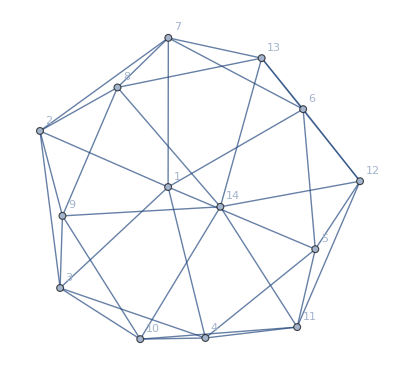

```mathematica
g2=Graph[plantri[[2]],VertexLabels->"Name"]
```

```mathematica
f2=FindFullFormula[g2];Length[f2]
```

854693

```mathematica
Sort[Tally[Map[PartitionType2[ #]&,Select[f2,StringCount[SymbolName[#],"x"]==3&]]]]
```

{{{4,4,3,3},19},{{4,4,4,2},1}}

```mathematica
Map[{N[StandardDeviation[#]],#}&,IntegerPartitions[14,{4}]]//Sort
```

{{0.57735,{4,4,3,3}},{1.,{4,4,4,2}},{1.,{5,3,3,3}},{1.29099,{5,4,3,2}},{1.73205,{5,4,4,1}},{1.73205,{5,5,2,2}},{1.73205,{6,3,3,2}},{1.91485,{5,5,3,1}},{1.91485,{6,4,2,2}},{2.08167,{6,4,3,1}},{2.38048,{6,5,2,1}},{2.38048,{7,3,2,2}},{2.51661,{7,3,3,1}},{2.64575,{7,4,2,1}},{2.88675,{6,6,1,1}},{3.,{7,5,1,1}},{3.,{8,2,2,2}},{3.10913,{8,3,2,1}},{3.31662,{8,4,1,1}},{3.69685,{9,2,2,1}},{3.78594,{9,3,1,1}},{4.3589,{10,2,1,1}},{5.,{11,1,1,1}}}

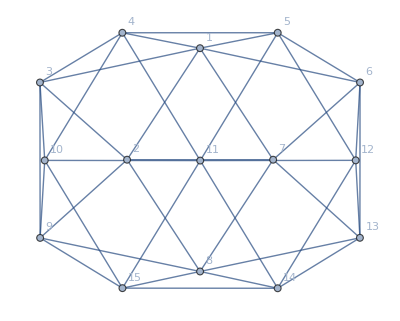

```mathematica
g3=Graph[plantri[[3]],VertexLabels->"Name"]
```

```mathematica
f3=FindFullFormula[g3];Length[f3]
```

5286481

```mathematica
Sort[Tally[Map[PartitionType2[ #]&,Select[f3,StringCount[SymbolName[#],"x"]==3&]]]]
```

{{{4,4,4,3},32}}

```mathematica
Sort[VertexList[g3]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
g4=Graph[plantri[[4]],VertexLabels->"Name"];VertexList[g4]//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
f4=FindFullFormula[g4];Length[f4]
```

$Aborted

```mathematica
Sort[Tally[Map[PartitionType2[ #]&,Select[f4,StringCount[SymbolName[#],"x"]==3&]]]]
```

```mathematica
Length[f1]
```

26793

```mathematica
TableForm[Sort[Tally[Map[PartitionType2[ #]&,f1]]],TableDepth->2]
```

{3,3,3,3} | 10
{3,3,2,2,2} | 420
{3,3,3,2,1} | 240
{2,2,2,2,2,2} | 368
{3,2,2,2,2,1} | 2520
{3,3,2,2,1,1} | 1920
{3,3,3,1,1,1} | 100
{2,2,2,2,2,1,1} | 3648
{3,2,2,2,1,1,1} | 5400
{3,3,2,1,1,1,1} | 960
{2,2,2,2,1,1,1,1} | 5160
{3,2,2,1,1,1,1,1} | 2640
{3,3,1,1,1,1,1,1} | 100
{2,2,2,1,1,1,1,1,1} | 2380
{3,2,1,1,1,1,1,1,1} | 420
{2,2,1,1,1,1,1,1,1,1} | 450
{3,1,1,1,1,1,1,1,1,1} | 20
{2,1,1,1,1,1,1,1,1,1,1} | 36
{1,1,1,1,1,1,1,1,1,1,1,1} | 1

```mathematica
TableForm[Sort[Tally[Map[PartitionType2[ #]&,f2]]],TableDepth->2]
```

{4,4,3,3} | 19
{4,4,4,2} | 1
{3,3,3,3,2} | 1319
{4,3,3,2,2} | 1494
{4,3,3,3,1} | 440
{4,4,2,2,2} | 53
{4,4,3,2,1} | 138
{4,4,4,1,1} | 1
{3,3,2,2,2,2} | 16921
{3,3,3,2,2,1} | 22560
{3,3,3,3,1,1} | 2015
{4,2,2,2,2,2} | 945
{4,3,2,2,2,1} | 6884
{4,3,3,2,1,1} | 3900
{4,4,2,2,1,1} | 195
{4,4,3,1,1,1} | 50
{2,2,2,2,2,2,2} | 4869
{3,2,2,2,2,2,1} | 63462
{3,3,2,2,2,1,1} | 101236
{3,3,3,2,1,1,1} | 22268
{4,2,2,2,2,1,1} | 6813
{4,3,2,2,1,1,1} | 9504
{4,3,3,1,1,1,1} | 840
{4,4,2,1,1,1,1} | 81
{2,2,2,2,2,2,1,1} | 53199
{3,2,2,2,2,1,1,1} | 162458
{3,3,2,2,1,1,1,1} | 76506
{3,3,3,1,1,1,1,1} | 3278
{4,2,2,2,1,1,1,1} | 6590
{4,3,2,1,1,1,1,1} | 2652
{4,4,1,1,1,1,1,1} | 7
{2,2,2,2,2,1,1,1,1} | 83859
{3,2,2,2,1,1,1,1,1} | 100868
{3,3,2,1,1,1,1,1,1} | 15540
{4,2,2,1,1,1,1,1,1} | 1938
{4,3,1,1,1,1,1,1,1} | 180
{2,2,2,2,1,1,1,1,1,1} | 44509
{3,2,2,1,1,1,1,1,1,1} | 22596
{3,3,1,1,1,1,1,1,1,1} | 855
{4,2,1,1,1,1,1,1,1,1} | 207
{2,2,2,1,1,1,1,1,1,1,1} | 10225
{3,2,1,1,1,1,1,1,1,1,1} | 1990
{4,1,1,1,1,1,1,1,1,1,1} | 7
{2,2,1,1,1,1,1,1,1,1,1,1} | 1107
{3,1,1,1,1,1,1,1,1,1,1,1} | 58
{2,1,1,1,1,1,1,1,1,1,1,1,1} | 55
{1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1